-Graphics3D-

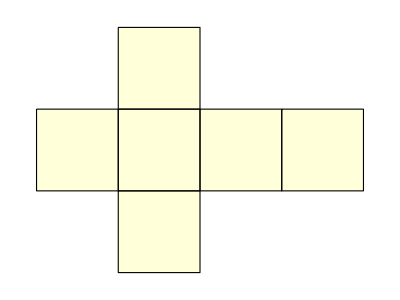

{{1,2},{1,3},{1,5},{2,4},{2,6},{3,4},{3,7},{4,8},{5,6},{5,7},{6,8},{7,8}}

-Graphics3D-

```mathematica
(* use cube function*)
Graphics3D[Cube[], Boxed->False]
PolyhedronData["Cube", "Net"]
vertices=PolyhedronData["Cube","VertexCoordinates"];
edges = PolyhedronData["Cube", "EdgeIndices"]
faces = PolyhedronData["Cube", "FaceIndices"];Graphics3D[{PolyhedronData["Cube","Faces"],Table[Text[Style[i,Bold,16],vertices[[i]]],{i,Length[vertices]}]},Boxed->False]
```